## §2. Функциональные ряды

### 2.1. Область сходимости функционального ряда

Пусть функции f_n(z), n∈ℕ, определены в области D. Выражение

f_1(z)+f_2(z)+...+f_n(z)+...=∑_(n=1)^∞ f_n(z), z∈D

называется функциональным рядом. Если для z_0∈D, числовой ряд ∑_(n=1)^∞ f_n(z_0) сходится, то говорим, что функциональный ряд (1) сходится в точке z_0. Если в каждой точке z∈D_1⊂D числовые ряды ∑_(n=1)^∞ f_n(z) сходятся, то ряд (1) называется сходящимся в области D_1.

К р и т е р и й  К о ш и. Для того чтобы функциональный ряд (1) был сходящимся в области D_1, необходимо и достаточно, чтобы для любого ϵ>0 и для любого z_0∈D_1, существовало N=N(ϵ, z), такое, что

|f_(n+1)(z)+f_(n+2)(z)+...+f_(n+p)(z)|<ϵ, для всех n>N(ϵ,z) и p∈ℕ.

Для определения области абсолютной сходимости функционального ряда (1) следует воспользоваться либо признаком Даламбера, либо признаком Коши. Именно, если:

lim_(n→∞) |(f_(n+1)(z))/(f_n(z))|=q(z)   или

lim_(n→∞) (|f_n(z)|)^(1/n)=q(z) ,

то для определения области абсолютной сходимости ряда (1) следует решить функциональное неравенство q(z)<1. При этом для изучения поведения ряда в граничных точках получаемой области, т.е. в точках, описываемых уравнением q(z)=1, требуется дополнительное исследование.

##### Пример №12.124

Найти область сходимости ряда (x∈ℝ). Исследовать ряд на абсолютную сходимость.

∑_(n=1)^∞ (-1)^n n^-x

Запишем общий член ряда:

```mathematica
f[n_,x_]:=(-1)^n n^-x
```

По признаку Лейбница данный ряд сходится при любых x| x>0, так как выполняются все необходимые условия.

На границе сходимости x=0 получим ряд:

∑_(n=1)^∞ (-1)^n

Данный ряд не является сходящимся, и следовательно область сходимости исходного ряда: x>0

Ряд, составленный из модулей будет выглядеть так:

∑_(n=1)^∞ 1/n^x

Данный ряд сходится абсолютно при x>1. Докажем это, используя интегральный признак Коши:

```mathematica
Integrate[1/n^x,{n,1,Infinity},Assumptions->x∈Reals]
```

ConditionalExpression[1/(-1+x),x>1]

Получили, что x >1. Следовательно, область сходимости данного ряда:  x∈(1,+∞).

##### Пример №12.125

Найти область сходимости ряда (x∈ℝ). Исследовать ряд на абсолютную сходимость.

∑_(n=1)^∞ (cos(n x))/(n √n)

Запишем член ряда:

```mathematica
f[n_,x_]:=Cos[n x]/n^(3/2)
```

Чтобы воспользоваться признаком Абеля-Дирихле необходимо доказать, что частичные суммы ряда ∑_(k=1)^n Cos(n x) ограничены в совокупности:

```mathematica
Sum[Cos[k x],{k,1,n}]
```

Cos[1/2 (1+n) x] Csc[x/2] Sin[(n x)/2]

Так как произведение Sin(a)Cos(b) по модулю не превосходит 1 при любых а и b, имеем:

|∑_(n=1)^∞ cos(n x)|≤ 1/(|sin(x/2)|)      x≠ 0

Что и требовалось доказать.

Так как ряд ∑_(n=1)^∞ 1/n^(3/2) сходится, то и исходный ряд:

∑_(n=1)^∞ (cos(n x))/(n √n)

по признаку Абеля-Дирихле сходится при любых x≠0. Следовательно область сходимости данного ряда: x ∈ℝ \ {0}

##### Пример №12.136

Найти область абсолютной сходимости ряда:

∑_(n=1)^∞ (n 2^n)/(z-3ⅈ)^(2n)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=(n 2^n)/(z-3I)^(2n)
```

Найдем область сходимости данного ряда по признаку Даламбера:

```mathematica
Limit[f[n+1,z]/f[n,z],n->Infinity]
```

2/(-3 ⅈ+z)^2

Получили, что исходный ряд сходится в кольце:

2/(|-3 ⅈ+z|^2)<1
|z-3ⅈ|^2>2
|z-3ⅈ| >√2

На границе области получаем следующий ряд:

∑_(n=1)^∞ (n 2^n)/(√2)^(2n)=∑_(n=1)^∞ n

Так как ряд на границе не сходится,  то областью сходимости исходного ряда будет: |z-3ⅈ| >√2

##### Пример №12.138

Найти область абсолютной сходимости:

∑_(n=1)^∞ 1/n^2 ⅇ^(-n z^2)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=1/n^2 Exp[-n z^2]
```

Для того чтобы определить область сходимости, воспользуемся признаком Коши:

```mathematica
Limit[f[n,z]^(1/n),n-> Infinity]
```

ⅇ^(-z^2)

Получаем условие:e^(-z^2)<1 ⇒ Re[z^2]≥ 0.

Из алгебраической формы записи z=x+I y, z^2=x^2-y^2+2I x y следует, что x^2-y^2≥ 0

Изобразим решение данного неравенства:

```mathematica
RegionPlot[x^2-y^2≥ 0,{x,-3,3},{y,-3,3},Axes->True,Frame->False]
```

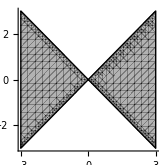

Из графика видно, что ряд сходится в: D={z| -π/4 ≤ arg(z)≤ π/4&& 3π/4≤ arg(z)≤ 5π/4}

С использованием описанных выше методов рекомендуется решить задания №№12.124-12.143.

### 2.2. Равномерная сходимость

Сходящийся в области D_1 функциональный ряд (1) называется равномерно сходящимся в этой области, если для любого ϵ>0 найдется N=N(ϵ) такое, что для остатка ряда (1)

R_n(z)=∑_(k=n+1)^∞ f_k(z)

при всех n>N(ϵ) и z∈D_1 имеет место оценка:

|R_n(z)|<ϵ

К р и т е р и й  К о ш и  р а в н о м е р н о й  с х о д и м о с т и. Для того чтобы функциональный ряд (1) был равномерно сходящимся в области D_1, необходимо и достаточно, чтобы для любого ϵ>0 существовало N=N(ϵ) такое, что для всех n>N(ϵ) и z∈D_1 выполнялись неравенства

|f_(n+1)(z)+f_(n+2)(z)+...+f_(n+p)(z)|<ϵ, p=1,2...

П р и з н а к  В е й е р ш т р а с с а. Пусть функциональный ряд (1) сходится в области D_1, и пусть существует сходящийся знакоположительный числовой ряд ∑_(n=1)^∞ a_n, такой, что для всех n>N_0 и z∈D_1 члены ряда (1) удовлетворяют условию:

|f_n(z)|≤ a_n

Тогда ряд (1) сходится абсолютно и равномерно в области D_1.

##### Пример №1

Исследовать функциональный ряд:

∑_(n=2)^∞ (2^n(z+3)^n)/(n (3 ln(n) +1)^2)

Запишем общий член ряда:

```mathematica
f[n_,z_]:=2^n/(n(3Log[n]+1)^2)(z+3)^n
```

Найдем область сходимости с помощью критерия Коши:

```mathematica
Limit[f[n,z]^(1/n),n-> Infinity]
```

2 (3+z)

Таким образом, область сходимости исследуемого ряда: |z+3|<1/2

На границе области сходимости при z=-2.5 получаем ряд:

∑_(n=2)^∞ (2^n(1/2)^n)/(n (3 ln(n) +1)^2)=∑_(n=2)^∞ 1/(n (3 ln(n) +1)^2)

По интегральному признаку Коши он сходится:

```mathematica
Integrate[f[n,-5/2],{n,2,Infinity}]
```

1/(3+Log[512])

Так как выполняется равенство:

|f_n(z)|=(2^n|z+3|^n)/(n (3 ln(n) +1)^2)≤ 1/(n (3 ln(n) +1)^2)

ряд (6) называется мажорирующим для исследуемого. Поэтому последний по признаку Вейерштрасса сходится равномерно в области |z+3|≤ 1/2.

##### Пример №12.151

Найти область сходимости и область равномерной сходимости указанного ряда:

∑_(n=1)^∞ 1/(n (z+2)^n)

Найдем область сходимости при помощи опции SumConvergence:

```mathematica
SumConvergence[1/(n(z+2)^n),n]
```

1/Abs[2+z]≤1&&1/(2+z)≠1

Ряд сходится в кольце |z+2| >1.

Для того чтобы найти область равномерной сходимости, поступим так: найдем область сходимости следующего ряда:

∑ 1/(n α^n),  lim_(n→∞) (1/(n α^n))^(1/n)=1/α<1

Так как данный ряд является мажорирующим для исходного функционального ряда:

|1/(n(z+2)^n)|≤ 1/(n α^n), где α>1

то, областью равномерной сходимости будет: |z+2| ≥ α>1